# 12 Conditioning

We want to be able to estimate what effect small changes in input have on the output in linear algebra problems

Algorithmic implementations always have clear input and output.

Some algorithms have more than one input and/or more than one output.

Since our inputs are vectors and/or matrices there are a variety of ways to measure the perturbation size.

Stability concerns perturbations of the input of an algorithmic implementation. This includes floating point arithmetic!

In an appropriate sense, small input changes produce small output changes for a stable algorithm.

Sometimes it is easier to think of a problem very abstractly as a function f:X→Y

As before some of these functions will have more than one input and/or more than one output. We lump all the inputs together as X  and all the outputs together as Y.

There are various possible measures for perturbation size.

Conditioning concerns perturbations of the input of an abstract function.

The function f is well conditioned at a point x^*∈X if small perturbations in x^* give small perturbations in f(x^*).

An ill-conditioned problem produces large perturbations in f(x^*) for some small perturbation in x^*.

It is possible to have an unstable algorithm for a well-conditioned problem!

## Condition Number

If f is differentiable we can write J(x)=Df(x) then δf=J(x).δx and

#### Absolute Condition Number κ̂ | = | lim_(δ->0) max_(||δx||<δ) (||f(x+δx)-f(x)||)/(||δx||) | = | max_δx (||δf||)/(||δx||)=max_δx (||J(x).δx||)/(||δx||)=||J(x)(||)_induced

#### Relative Condition Number κ | = | lim_(δ->0) sup_(||δx||<δ) (||f(x+δx)-f(x)||/||f(x)||)/(||δx||/||x||) | = | sup_δx (||δf||/||f(x)||)/(||δx||/||x||)=(||J(x)(||)_ind)/(||f(x)||/||x||)

As usual we care more about precision than we do accuracy. Relative condition numbers are much more important than absolute condition numbers!

A problem is well conditioned if k is small (say less than 10^2) and badly conditioned if k is big (say bigger than 10^10).

## Condition Number of f:ℝ→ℝ

We have formulas if f is smooth
	κ̂(x)=sup_δx (||f'(x) δx||)/(||δx||)=|f'(x)|
and 
	κ(x)=sup_δx (||f'(x) δx||/||f(x)||)/(||δx||/||x||)=|f'(x)|×(|x|)/(|f(x)|)

## Condition Number of f:ℝ^n→ℝ^m

We have formulas if f is smooth and we use the Euclidean norms to measure perturbations in the input space ℝ^n and the output space ℝ^m.
	κ̂(x)=sup_δx (||Df(x).δx||)/(||δx||)=sup_δx (||J(x).δx||)/(||δx||)=||J(x)(||)_induced=σ_1
and 
	κ(x)=sup_δx (||Df(x) .δx||/||f(x)||)/(||δx||/||x||)=σ_1×(|x|)/(|f(x)|).

## Condition Number of x→A.x with A∈ℝ^(m×m)

This linear map is smooth. With σ_(1:m) the thick singular values of A and Euclidean norms for the input space ℝ^m and output space ℝ^m we have
	κ̂(x)=σ_1
and 
	κ(x)=σ_1×(||x||)/(||A.x||)≤σ_1×max_(||x||) (||x||)/(||A.x||)=σ_1/σ_m
The condition number of a square matrix is defined to be the ratio of the largest singular value to the smallest singular value.  For A∈ℝ^(m×m) everyone writes 
	K(A)=σ_1/σ_m.
Note if A is not invertible σ_m=0. The condition number of a non-invertible square matrix is ∞.

## Condition Number of solving A.x=b→x with A∈ℝ^(m×m)

This map is smooth with two inputs (A and b) and provided A is invertible we can write it as 
	(A,b)→x=A^-1 b	 
Again write σ_(1:m) for the thick singular values of A and of course use Euclidean norms.

The sensitivity with respect to b is similar to the earlier computation
	(κ̂)_b(A,b)=max(1/σ_(1:m))=1/σ_m
and 
	κ_b(A,b)=1/σ_m×(||b||)/(||A^-1.b||)≤1/σ_m×max_(||b||) (||b||)/(||A^-1.b||)=1/σ_m×1/min[1/σ_(1:m)]=1/σ_m×1/(1/σ_1)=σ_1/σ_m
This is not a typo take a look at the definition and note that 
	κ(A^-1)=κ(A).

Sensitivity with respect to A→A+δA looks slightly different.  We could start from the derivative definitions but we are going to start with the perturbed equation with a fixed b
	(A+δA).(x+δx)=b  
and expand to get
	A.x+δA.x+A.δx+δA.δx=b.
Since A.x=b we have
	  δA.x+A.δx+δA.δx=0
and since δx→0  as δA→0 the quadratic term δA.δx is negligible in the limit and 
	δA.x+A.δx≈0
or in other words 
	δx≈-A^-1.δA.x.
This is all OK because we are considering small perturbations:  it is why we have the limit as δ→0 in our definitions!  When our perturbations are sufficiently small we have
	||δx||≤||A^-1(||)_induced||δA(||)_induced||x||.
There are actually perturbations δA that make ||δx||=||A^-1(||)_induced||δA(||)_induced||x||. If we put this all together we get 
	(||δx||/||x||)/(||δA||/||A||)≤(||A^-1||)/(1/||A||)=||A^-1||||A||=σ_1/σ_m=κ(A)
In other words the relative condition number of solving A.x=b with respect to perturbations δA in A is simply this matrix condition number.  Not all condition numbers are just the ratio of the singular values!

## Condition Numbers Matter!

The m×m Hilbert matrix 
	H_(i,j)=1/(i+j-1)
is a symmetric positive definite matrix with a formula for its inverse!  It also has a rapidly growing condition number!

```mathematica
m=5;
H=Table[1/(i+j-1),{i,m},{j,m}];
TabView[{
"H"->MatrixForm[H],
"H^-1"->MatrixForm[Inverse[H]]}]
```

12

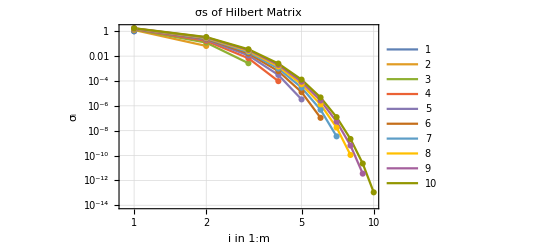

```mathematica
σs=Table[
H=Table[1/(i+j-1),{i,m},{j,m}];
SingularValueList[N[H]],
{m,1,10}];
ListLogLogPlot[σs,
PlotLabel->"σs of Hilbert Matrix",
PlotLegends->Automatic,
Joined->True,Mesh->All,FrameLabel->{"i in 1:m","σ_i"},
Frame->True,GridLines->Automatic]
```

Since the small singular values get tiny the matrices become badly conditioned.  Here is the message and result we get if we try to solve a linear system with a Numerical Hilbert matrix!

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.5,0.333333,0.25,0.2,0.166667,0.142857,0.125,0.111111,0.1},«8»,{0.1,0.0909091,0.0833333,«5»,0.0555556,0.0526316}} may contain significant numerical errors.

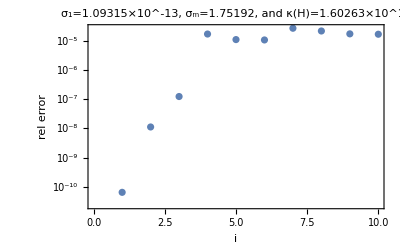

```mathematica
m=10;
H=Table[1/(i+j-1),{i,m},{j,m}];
{σ1,σm}=N[MinMax[SingularValueList[N[H,256]]]];
xIn=RandomInteger[{1,20},m];
b=H.xIn;
xOut=LinearSolve[N[H],b];
ListLogPlot[Abs[(xIn-xOut)/xIn],Frame->True, GridLines->Automatic,
FrameLabel->{"i","rel error"},
PlotLabel->StringForm["σ_1=``, σ_m=``, and κ(H)=``",σ1,σm,σm/σ1]]
```

## Conclusions

You should take such warnings seriously.  The condition number basically tells you the damage (as an error multiplier) that your computation suffers as a result of the linear solve.  If the condition number is 10^6 you have amplified “errors” by 10^6!  The basic double precision round off error starts out at roughly 10^-16 so after using a matrix with condition number 10^6 your new error is roughly 10^-10.  Using such a matrix took you from 16 decimal places to 10 decimal places! Do it again and you lose another six taking you down to an embarrassing 4 decimal places. Do it a third time and your computation is worthless!

## Plan

Wherever possible you should compute with orthogonal matrices Q which satisfy κ(Q)=1 and do not amplify round off errors. If you compute with something other than orthogonal matrices you should try to estimate the condition number and warn users if they could be about to do something stupid.